```mathematica
mecSquared = 0.511*10^6;
hbarC = 197.33 * 10^6*10^(-15);
e0 = -13.6;
e0Abs = Abs[e0];
a0 = 0.529*10^(-10);
```

```mathematica
kappaSquared = (2*mecSquared/(hbarC)^2)*e0Abs
```

3.56947×10^20

```mathematica
kSquared[v_] := (2*mecSquared/(hbarC)^2)*(v-e0Abs);
z0Squared[v_]:= (2*mecSquared/(hbarC)^2)*a0^2*v;
eta[v_]:= Sqrt[kSquared[v]]*a0;
xi:=Sqrt[kappaSquared]*a0;
```

{}

```mathematica
FindRoot[{xi-eta[v]*Tan[eta[v]]==0}, {v, 0, 400}]
```

{v→23.6735}

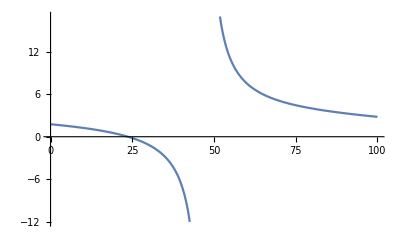

```mathematica
Plot[xi-eta[v]*Tan[eta[v]], {v,0, 100}]
```

```mathematica
v0=23.67
xi-eta[v0]*Tan[eta[v0]]
```

23.67

0.000476626

```mathematica
Sqrt[z0Squared[23]]
```

1.29973

```mathematica
Sqrt[eta[23]^2+xi^2]
```

1.02376

```mathematica
v0 = 23.67;
kappaSquaredE[e_] := (2*mecSquared/(hbarC)^2)*Abs[e];
kSquaredE[e_] := (2*mecSquared/(hbarC)^2)*(v0-Abs[e]);
z0SquaredE:= (2*mecSquared/(hbarC)^2)*a0^2*v0;
etaE[e_]:= Sqrt[kSquaredE[e]]*a0;
xiE[e_]:=Sqrt[kappaSquaredE[e]]*a0;
```

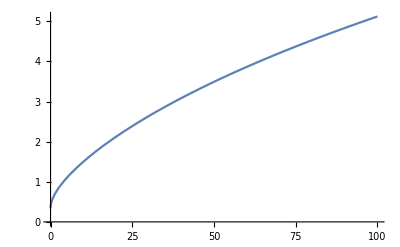

```mathematica
Plot[xiE[e]+etaE[e]*Cot[etaE[e]], {e,0, 100}]
```

```mathematica
FindRoot[{xiE[e]-etaE[e]*Tan[etaE[e]]==0}, {e, 400}]
```

{e→13.5972+0. ⅈ}

```mathematica
xi1=5.674526;
xi2=3.398324;
z0=2*Pi;
e1toV0 = (xi1/z0)^2
e2toV0 = (xi2/z0)^2
```

0.815642

0.29253

```mathematica
N@First[Solve[{x^2+y^2==(2*Pi)^2, x*Cot[x] == -y*Coth[y], x> 0, x<2*Pi, y>0, y< 2*Pi}, {x,y}]]
```

{x→2.69781,y→5.67453}

```mathematica
(2.6978073887797653/(2*Pi))^2//N
```

0.184358

```mathematica
N@Second[Solve[{x^2+y^2==(2*Pi)^2, x*Cot[x] == -y*Coth[y], x> 0, x<2*Pi, y>0, y< 2*Pi}, {x,y}]]
```

Second[{{x→2.69781,y→5.67453},{x→5.28487,y→3.39832}}]

```mathematica
(5.284865694831296/(2*Pi))^2
```

0.70747

```mathematica
psi1[x_]:=Sqrt[1/3]*Sqrt[2/a]*Sin[2*Pi*x/a]*E^(-I*t*alpha*4);
psi2[x_]:=Sqrt[2/3]*Sqrt[2/a]*Sin[3*Pi*x/a]*E^(-I*t*alpha*9);
psi1C[x_]:=Sqrt[1/3]*Sqrt[2/a]*Sin[2*Pi*x/a]*E^(I*t*alpha*4);
psi2C[x_]:=Sqrt[2/3]*Sqrt[2/a]*Sin[3*Pi*x/a]*E^(I*t*alpha*9);

Integrate[(psi1C[x]+psi2C[x])*x*(psi1[x]+psi2[x]), {x,0,a}]//Simplify
```

1/50 a (25-(64 √2 Cos[5 alpha t])/π^2)

```mathematica
Integrate[(psi1C[x]+psi2C[x])*hbar/I*(psi1'[x]+psi2'[x]), {x,0,a}]//Simplify
```

(16 √2 hbar Sin[5 alpha t])/(5 a)

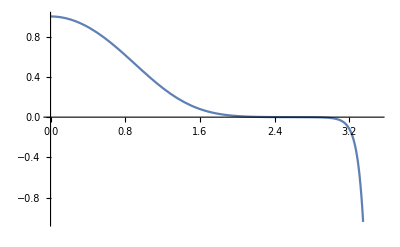

```mathematica
Clear[e, psi]
v[x_] := x^4;
e=0.6679865;
psi = psi/. NDSolve[{-(1/2)psi''[u]+(v[u]-e)psi[u] == 0, psi[0]==1, psi'[0] == 0}, psi, {u,0,3.5}][[1]];
Plot[psi[u], {u, 0, 3.5}]
```